```mathematica
(*Set your own home directories up here:*)

mdwnt ="/home/simonfreedman/scratch-midway/cytomod/out/network/";
mdwkv ="/home/simonfreedman/scratch-midway/cytomod/out/kovar/";
mdwpl="/home/simonfreedman/scratch-midway/cytomod/out/pl/";
mdwtest="/home/simonfreedman/Code/cytomod/out/test/";
mdwtmp="/home/simonfreedman/Code/cytomod/out/tmp/";
mdwsarc="/home/simonfreedman/scratch-midway/cytomod/out/sarcomeric/";
archivent = "/project/weare-dinner/simonfreedman/cytomod/out/network/";
archivepl = "/project/weare-dinner/simonfreedman/cytomod/out/pl/";
archivesh = "/project/weare-dinner/simonfreedman/cytomod/out/shear/";
archivemot = "/project/weare-dinner/simonfreedman/cytomod/out/motility/";
archiveact = "/project/weare-dinner/simonfreedman/cytomod/out/active/";
archivea = "/project/weare-dinner/simonfreedman/cytomod/out/a_actinin/";
archivef = "/project/weare-dinner/simonfreedman/cytomod/out/filamin/";


(*Line Types*) 

(*link[l_]:=Graphics[
{(*Orange*)Red,
Arrowheads[0.004],
Arrow[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
}
];*)
link[l_,maxLength_:100]:=Graphics[
{Red,
Thick,
If[Norm[l[[3;;4]]]<maxLength,
Line[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}],
Point[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
]
}
];
polarLink[l_,maxLength_:4,loIndex_:0]:=Graphics[
{If[Length[l]≥6&&l[[6]]==loIndex,Blue,Red],
Arrowheads[0.04],
Thick,
If[Norm[l[[3;;4]]]<maxLength,
Arrow[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}],
Point[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
]
}
];
whiteLink[l_]:=Graphics[
{White,
Arrowheads[0.004],
Arrow[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
}
];
actin[a_,col_]:=Graphics[
{col,
Disk[{a[[1]],a[[2]]},a[[3]]]
}
];
radactin[a_,col_,rad_]:=Graphics[
{col,
Disk[{a[[1]],a[[2]]},rad]
}
];
amotor[l_,maxLength_:2]:=Graphics[
{(*If[Or[l[[5]]==-1, l[[6]]==-1],Green,Brown],Red*)Green,
Thickness[0.01],
If[Norm[l[[3;;4]]]<maxLength,
Line[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}],
Point[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
]
}
];
pmotor[l_]:=Graphics[
{(*If[Or[l[[5]]==-1, l[[6]]==-1],Blue,Black],Cyan*)Cyan,
Opacity[1],
Thickness[0.01],
(*Arrowheads[{-0.005,0.005}],*)
Line[{{l[[1]],l[[2]]},{l[[1]]+l[[3]],l[[2]]+l[[4]]}}]
}
];

(*
Simulator function
This function takes three parameters: 
d (String) is the directory that contains the txt_stack folder with the appropriate files :
  "rods.txt", 
"amotors.txt", 
"pmotors.txt"
Which were generated when the simulation was run.
deltat (integer) is the number of frames between each run
genMovie (True or False) is a flag. If set True, the function generates a file called movie.avi in the <d>/data/ file. 
This function returns the frames of the movie requested. 
*)
```

```mathematica
ClearAll[sim]
sim[actins_,links_,amotors_,pmotors_,dir_,movieFlag_,fov_:{500,500},dt_:1,polar_:True,np_:11,acolor_:Red]:=
Module[
{},
(*Generate Image Time Series, make into movie*)
frames={};
If[actins≠{},AppendTo[frames,Map[actin[#,acolor]&,actins,{2}]]];
If[links≠{},AppendTo[frames,Map[link[#,Abs[Min[fov]/2]]&,links,{2}]]];
If[amotors≠{},AppendTo[frames,Map[amotor,amotors,{2}]]];
If[pmotors≠{},AppendTo[frames,Map[pmotor,pmotors,{2}]]];
If[polar,
If[actins≠{},
AppendTo[frames,Map[actin[#,Blue]&,actins[[All,1;;-1;;np]],{2}]],
If[links≠{},
rad=Mean[Flatten[Map[Norm,links[[All,All,3;;4]],{2}]]]/6;
AppendTo[frames,Map[radactin[#,Blue,rad]&,links[[All,1;;-1;;np-1]],{2}]]
]
]
];
frames=Transpose[frames];
minx=0;miny=0;maxx=0;maxy=0;
If[
TensorRank[fov]==1,
minx=-fov[[1]]/2;maxx=fov[[1]]/2;miny=-fov[[2]]/2;maxy=fov[[2]]/2,
minx=fov[[1,1]];maxx=fov[[1,2]];miny=fov[[2,1]];maxy=fov[[2,2]]
];
frames=Map[
Show[#,
Frame->True,
Background->White,
PlotRange->{{minx,maxx},{miny,maxy}},
(*FrameLabel->{"x (μm)","y (μm)","t = "<>ToString[dt*skipFrames*(t-1)]<>" s "},*)
FrameTicks->None,
Ticks->None,
BaseStyle->{FontSize->24,FontColor->Black}
]&
,frames
];
If[movieFlag, Export[dir<>"/data/movie.avi",frames]];
frames
];
ClearAll[simLE];
simLE[actins_,links_,amotors_,pmotors_,dir_,movieFlag_,fov_:{500,500},dt_:1,acolor_:Red,cell_:{0,0},strainPct_:0]:=
Module[
{actinsr=actins, linksr=links,amotorsr=amotors,pmotorsr=pmotors},
(*Generate Image Time Series, make into movie*)
δrx=strainPct*fov[[1]]*cell[[2]];
cm=fov*cell;
minx=fov[[1]](cell[[1]]-0.5);
maxx=fov[[1]](cell[[1]]+0.5);
miny=fov[[2]](cell[[2]]-0.5);
maxy=fov[[2]](cell[[2]]+0.5);
frames={};
If[actinsr≠{},
actinsr[[All,All,1;;2]]=Map[ (#+cm+{δrx,0})&,actinsr[[All,All,1;;2]],{2}];AppendTo[frames,Map[actin[#,Blend[{acolor,Red},Part[#,5]/10.]]&,actinsr,{2}]]];
If[linksr≠{},
linksr[[All,All,1;;2]]=Map[ (#+cm+{δrx,0})&,linksr[[All,All,1;;2]],{2}];
AppendTo[frames,Map[link,linksr,{2}]]];
If[amotorsr≠{},
amotorsr[[All,All,1;;2]]=Map[(#+cm+{δrx,0})&,amotorsr[[All,All,1;;2]],{2}];
AppendTo[frames,Map[amotor,amotorsr,{2}]]];
If[pmotorsr≠{},
pmotorsr[[All,All,1;;2]]=Map[(#+cm+{δrx,0})&,pmotorsr[[All,All,1;;2]],{2}];AppendTo[frames,Map[pmotor,pmotorsr,{2}]]];
frames=Transpose[frames];
minx=0;miny=0;maxx=0;maxy=0;
frames=Map[
Show[#,
Frame->True,
Background->White,
PlotRange->{{minx,maxx},{miny,maxy}},
(*FrameLabel->{"x (μm)","y (μm)","t = "<>ToString[dt*skipFrames*(t-1)]<>" s "},*)
FrameTicks->None,
Ticks->None,
BaseStyle->{FontSize->24,FontColor->Black}
]&
,frames
];
If[movieFlag, Export[dir<>"/data/movie.avi",frames]];
frames
];
pts[dir_,name_]:=ToExpression[Import[dir<>"/txt_stack/"<>name<>".dat","TSV"]];
```

## More Functions

```mathematica
pincrds[crds_]:=
Module[
{},
cms = crds[[All,1]];(*(crds[[All,1]]+crds[[All,2]])/2.;*)
dr1=crds[[All,2]]-crds[[All,1]];
(*dr2=crds[[All,3]]-crds[[All,2]];
angles=ArcTan[dr2[[All,1]],dr2[[All,2]]]-ArcTan[dr1[[All,1]],dr1[[All,2]]];*)
angles=ArcTan[dr1[[All,1]],dr1[[All,2]]];
(*angles=angles-2Pi Floor[angles/2Pi+0.5];*)
dispcrds=Table[Map[(#-cms[[t]])&,crds[[t]]],{t,1,Length[crds]}];
rotcrds=Table[
Join[{dispcrds[[t,1]]},Map[(RotationMatrix[-angles[[t]]].#)&,dispcrds[[t,2;;]]]],
{t,Length[dispcrds]}
];
rotcrds
];

simpinned[dir_,skipFrames_,movieFlag_,fov_:{500,500},dt_:1]:=
Module[
{},
(*Load Data*)
at=ParticleTimeSeries[dir,"actins",-1,4,skipFrames-1];
crds=pincrds[at[[1;;100,All,1;;2]]];
Print["Generating frames for directory "<>dir];
(*Generate Image Time Series, make into movie*)
DistributeDefinitions[crds];
frames=ParallelTable
[
Show[
Join[
Table[
actin[crds[[t,i]]],
{i,Length[crds[[t]]]}
]
],
Frame->True,
Background->Black,
PlotRange->{{-fov[[1]]/2,fov[[1]]/2},{-fov[[2]]/2,fov[[2]]/2}},
FrameLabel->{"x (μm)","y (μm)","t = "<>ToString[dt*skipFrames*(t-1)]<>" s "},
Ticks->None,
(*FrameTicks->None,*)
BaseStyle->{FontSize->24,FontColor->Black}
]
,{t,1,Length[crds]}
];
If[movieFlag, Export[dir<>"/data/movie.avi",frames]];
frames
];
simgs[dir_,skipFrames_,movieFlag_,fov_:{500,500},dt_:1]:=
Module[
{},
(*Load Data*)
lt=ParticleTimeSeries[dir,"links"];
lt=lt[[1;;-1;;skipFrames]];
Print["Generating frames for directory "<>dir];
(*Generate Image Time Series, make into movie*)
DistributeDefinitions[lt];
frames=ParallelTable
[
Show[
Table[
whiteLink[lt[[t,i]]],
{i,Length[lt[[t]]]}
]
,Background->Black,PlotRange->{{-fov[[1]]/2,fov[[1]]/2},{-fov[[2]]/2,fov[[2]]/2}}
]
,{t,1,Length[lt]}
];
If[movieFlag, 
Do[Export[dir<>"/data/tiffs/t"<>ToString[i]<>".tif",frames[[i]]],{i,Length[frames]}]
];
frames
];
simMotors[dir_,skipFrames_,movieFlag_,fov_:{500,500},dt_:1]:=
Module[
{},
(*Load Data*)
pmt=ParticleTimeSeries[dir,"pmotors",-1,8,skipFrames-1]; 
amt=ParticleTimeSeries[dir,"amotors",-1,8,skipFrames-1];
Print["Generating frames for directory "<>dir];
(*Generate Image Time Series, make into movie*)
maxFrame = Min[Length[pmt], Length[amt]];
frames=ParallelTable
[
Show[
Table[
amotor[amt[[t,i]]],
{i,Length[amt[[t]]]}
],
Table[
pmotor[pmt[[t,i]]],
{i,Length[pmt[[t]]]}
],
Frame->True,Background->White,PlotRange->{{-fov[[1]]/2,fov[[1]]/2},{-fov[[2]]/2,fov[[2]]/2}},FrameLabel->{"x (μm)","y (μm)","t = "<>ToString[dt*skipFrames*(t-1)]<>" s "},BaseStyle->{FontSize->16,FontColor->Black}
],
{t,maxFrame}
];
If[movieFlag, 
Do[Export[dir<>"/data/tiffs/t"<>ToString[i]<>".tif",frames[[i]]],{i,Length[frames]}]
];
frames
];
simMotors[dir_,skipFrames_,movieFlag_,fov_:{500,500},dt_:1]:=
Module[
{},
(*Load Data*)
pmt=ParticleTimeSeries[dir,"pmotors",-1,8,skipFrames-1]; 
amt=ParticleTimeSeries[dir,"amotors",-1,8,skipFrames-1];
Print["Generating frames for directory "<>dir];
(*Generate Image Time Series, make into movie*)
maxFrame = Min[Length[pmt], Length[amt]];
frames=ParallelTable
[
Show[
Table[
amotor[amt[[t,i]]],
{i,Length[amt[[t]]]}
],
Table[
pmotor[pmt[[t,i]]],
{i,Length[pmt[[t]]]}
],
Frame->True,Background->White,PlotRange->{{-fov[[1]]/2,fov[[1]]/2},{-fov[[2]]/2,fov[[2]]/2}},FrameLabel->{"x (μm)","y (μm)","t = "<>ToString[dt*skipFrames*(t-1)]<>" s "},BaseStyle->{FontSize->16,FontColor->Black}
],
{t,maxFrame}
];
If[movieFlag, 
Export[dir<>"/data/mmovie.avi",frames]
];
frames
];
simPR[dir_,skipFrames_,movieFlag_,pr_:{{-25,25},{-25,25}},dt_:1]:=
Module[
{},
(*Load Data*)
pmt=ParticleTimeSeries[dir,"pmotors",-1,8,skipFrames-1]; 
amt=ParticleTimeSeries[dir,"amotors",-1,8,skipFrames-1];
lt=ParticleTimeSeries[dir,"links",-1,5,skipFrames-1];

maxFrame=Max[Length[amt],Length[pmt],Length[rt],Length[lt]];
Print["Generating frames for directory "<>dir];
(*Generate Image Time Series, make into movie*)
DistributeDefinitions[rt,lt,pmt,amt,maxFrame];
frames=ParallelTable
[
Show[
Join[
If[Length[amt]≥t,
Table[
amotor[amt[[t,i]]],
{i,Length[amt[[t]]]}
],{}
],
If[Length[pmt]≥t,
Table[
pmotor[pmt[[t,i]]],
{i,Length[pmt[[t]]]}
],{}
],
If[Length[lt]≥t,
Table[
link[lt[[t,i]]],
{i,Length[lt[[t]]]}
],{}
]
]
,Frame->True,Background->White,PlotRange->pr,PlotRangeClipping->True,FrameLabel->{"x (μm)","y (μm)","t = "<>ToString[dt*skipFrames*(t-1)]<>" s "},BaseStyle->{FontSize->16,FontColor->Black}
]
,{t,1,maxFrame}
];
If[movieFlag, Export[dir<>"/data/movie.avi",frames]];
Clear[lt,amt,pmt];
frames
];
zeroTraj[ct_,zerodIndexes_:{1,2}]:=
Module[{},
minctx= Min/@ct[[All,All,1]];
mincty=Min/@ct[[All,All,2]];
ctx = Table[ct[[t,All,1]]-minctx[[t]],{t,1,Length[ct]}];
cty=Table[ct[[t,All,2]]-mincty[[t]],{t,1,Length[ct]}];
ctnew=Table[
Map[
Flatten,
Transpose[{ctx[[t]],cty[[t]],ct[[t,All,3;;-1]]}]
],
{t,1,Length[ct]}
];
ctnew
];
simZeroed[dir_,skipFrames_,movieFlag_,fov_:{500,500},dt_:1,endframe_:-1]:=
Module[
{},
(*Load Data*)
pmt=pinTraj[ParticleTimeSeries[dir,"pmotors",-1,8,skipFrames-1,1,endframe]];
amt={};
(*amt=ParticleTimeSeries[dir,"amotors",-1,8,skipFrames-1,1,endframe];*)
lt=pinTraj[ParticleTimeSeries[dir,"links",-1,5,skipFrames-1,1,endframe]];
maxFrame=Max[Length[amt],Length[pmt],Length[lt]];
Print["Generating "<>ToString[maxFrame]<>" frames for directory "<>dir];
(*Generate Image Time Series, make into movie*)
frames=Table
[
Show[
Join[
If[Length[lt]≥t,
Table[
link[lt[[t,i]]],
{i,Length[lt[[t]]]}
],{}
],
If[Length[pmt]≥t,
Table[
pmotor[pmt[[t,i]]],
{i,Length[pmt[[t]]]}
],{}
],
If[Length[amt]≥t,
Table[
amotor[amt[[t,i]]],
{i,Length[amt[[t]]]}
],{}
]
],
Frame->True,
Background->White,
PlotRange->{{-fov[[1]]/2,fov[[1]]/2},{-fov[[2]]/2,fov[[2]]/2}},
(*FrameLabel->{"x (μm)","y (μm)","t = "<>ToString[dt*skipFrames*(t-1)]<>" s "},*)
FrameTicks->None,
Ticks->None,
BaseStyle->{FontSize->24,FontColor->Black}
]
,{t,1,maxFrame}
];
If[movieFlag, Export[dir<>"/data/movie.avi",frames]];
Clear[lt,amt,pmt];
frames
];
```

```mathematica
lastframe[dir_,skipFrames_,movieFlag_,fov_:{500,500},dt_:1,endframe_:-1]:=
Module[
{},
(*Load Data*)
lt=ParticleTimeSeries[dir,"links",-1,5,1,1,endframe];

pmt=ParticleTimeSeries[dir,"pmotors",-1,8,skipFrames-1,1,endframe]; 
amt={};
(*amt=ParticleTimeSeries[dir,"amotors",-1,8,skipFrames-1,1,endframe];*)

maxFrame=Max[Length[amt],Length[pmt],Length[lt]];
Print["Generating "<>ToString[maxFrame]<>" frames for directory "<>dir];
(*Generate Image Time Series, make into movie*)
frames=Table
[
Show[
Join[
If[Length[lt]≥t,
Table[
link[lt[[t,i]]],
{i,Length[lt[[t]]]}
],{}
],
If[Length[pmt]≥t,
Table[
pmotor[pmt[[t,i]]],
{i,Length[pmt[[t]]]}
],{}
],
If[Length[amt]≥t,
Table[
amotor[amt[[t,i]]],
{i,Length[amt[[t]]]}
],{}
]
],
Frame->True,
Background->White,
PlotRange->{{-fov[[1]]/2,fov[[1]]/2},{-fov[[2]]/2,fov[[2]]/2}},
(*FrameLabel->{"x (μm)","y (μm)","t = "<>ToString[dt*skipFrames*(t-1)]<>" s "},*)
FrameTicks->None,
Ticks->None,
BaseStyle->{FontSize->24,FontColor->Black}
]
,{t,1,maxFrame}
];
If[movieFlag, Export[dir<>"/data/movie.avi",frames]];
Clear[lt,amt,pmt];
frames
];
```

## Test Directory

```mathematica
act=pts[mdwtest,"actins"];
amotors=pts[mdwtest,"amotors"];
pmotors=pts[mdwtest,"pmotors"];
lks=pts[mdwtest,"links"];
```

```mathematica
pr=10{{-1,1},{-1,1}};
```

```mathematica
testfrs=sim[{},links[[2]],{},pmotors[[2]],"out/test",False,pr,1,False];
```

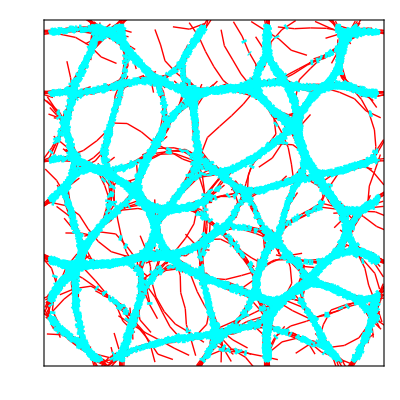
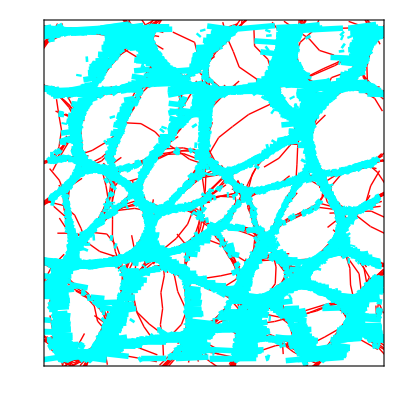
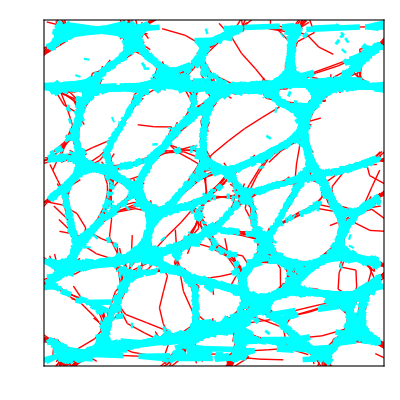

```mathematica
testfrs[[{1,2,-1}]]
```

```mathematica
Export["plots/fene/L20_100pN_fene.avi",testfrs];
```

```mathematica
Export["plots/fene/L20_100pN_hookean.avi",testfrs2];
```

```mathematica
Manipulate[testfrs[[t]],{t,1,Length[testfrs],1}]
```

## Shear Test Directory

```mathematica
nbds=4;
linkLength=2;
grid={(nbds-0.5)*linkLength,(nbds-1)linkLength Sqrt[3]/2};
skips=100;
dt=0.1;
delT=dt*skips;
Tf=1000;
tstrain=0.05;
delrx=tstrain*grid[[2]]*delT/Tf;
ksp=1;
keff=ksp/2.;
area=(nbds-1)^2*linkLength^2*Sqrt[3]/2;
```

```mathematica
fs=simSerial[mdwtest,100,False,grid+1,1];
```

Finished importing /home/simonfreedman/Code/cytomod/out/test//txt_stack/pmotors.txt

Finished importing /home/simonfreedman/Code/cytomod/out/test//txt_stack/links.txt

Generating 101 frames for directory /home/simonfreedman/Code/cytomod/out/test/

```mathematica
border[t_]:=Graphics[{EdgeForm[Directive[Thick,Dashed,Black]],
White,
Parallelogram[-grid/2-{delrx2/2*(t-1),0},{{grid[[1]],0},{2*delrx2*(t-1)/2,grid[[2]]}}]}];
```

```mathematica
fsb=Table[Show[
border[t],
fs[[t]],
PlotRange->{-grid/2-1,grid/2+1}ᵀ
],{t,1,Length[fs],1}];
```

```mathematica
Export[mdwsh<>"/tri/lattice4/data/movie.avi",fsb];
```

```mathematica
Manipulate[
Show[
border[t],
fs[[t]],
(*Graphics[Circle[{-4.5,-grid[[2]]/2},0.25]],Graphics[Circle[{2.5,-grid[[2]]/2},0.25]],*)PlotRange->{-grid/2-1,grid/2+1}ᵀ
],{t,1,Length[fs],1}]
```

```mathematica
Graphics[Orange
```

```mathematica
fs[[-1]]
```

```mathematica
fsz=simZeroed[mdwtest,100,False,2*{20.001,9Sqrt[3]},1];
```

Finished importing /home/simonfreedman/Code/cytomod/out/test//txt_stack/pmotors.txt

Finished importing /home/simonfreedman/Code/cytomod/out/test//txt_stack/links.txt

Generating 101 frames for directory /home/simonfreedman/Code/cytomod/out/test/

```mathematica
fs[[1;;-1]]
```

```mathematica
fsz[[1;;-1;;20]]
```

```mathematica
Export[mdwtest<>"/data/movie.avi",fs[[1;;200]]]
```

/home/simonfreedman/Code/cytomod/out/test//data/movie.avi

```mathematica
rt
```

## Other Directories

```mathematica
kbs={"0.001","0.01","0.1","1"};
pps=ToString/@Range[0,10];
dirsLo=
Table[archivent <>"flexible_fast2/kb0.01_pp"<>pp,{pp,pps}];
dirsHi=
Table[archivent<>"flexible_fast2/kb1_pp"<>pp,{pp,pps}];
```

```mathematica
fscont2=sim[dirsLo[[1]],1000,False,{10,10},0.1];
```

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/network/flexible_fast2/kb0.01_pp0/txt_stack/pmotors.txt

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/network/flexible_fast2/kb0.01_pp0/txt_stack/amotors.txt

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/network/flexible_fast2/kb0.01_pp0/txt_stack/links.txt

Generating frames for directory /project/weare-dinner/simonfreedman/cytomod/out/network/flexible_fast2/kb0.01_pp0

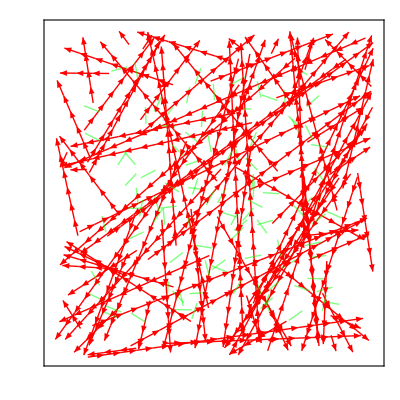
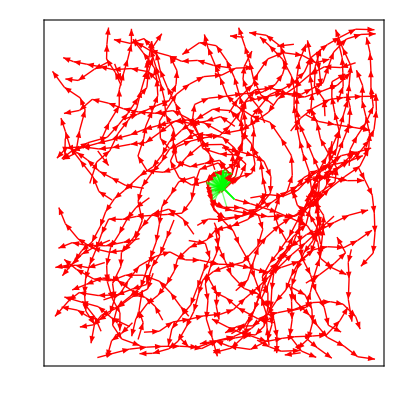
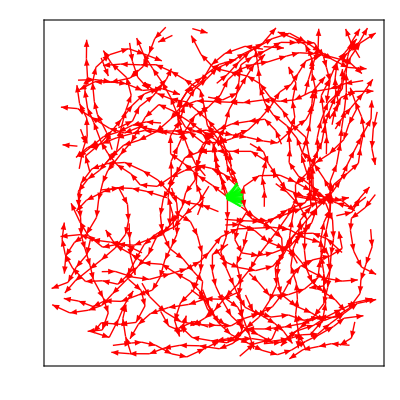

```mathematica
fscont2[[{1,6,21}]]
```

```mathematica
fspol=sim[dirsHi[[1]],1000,False,{10,10},0.1];
```

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/network/flexible_fast2/kb1_pp0/txt_stack/pmotors.txt

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/network/flexible_fast2/kb1_pp0/txt_stack/amotors.txt

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/network/flexible_fast2/kb1_pp0/txt_stack/links.txt

Generating frames for directory /project/weare-dinner/simonfreedman/cytomod/out/network/flexible_fast2/kb1_pp0

```mathematica
Export["plots/net4pap/kb01_pp0_t0.svg",fscont2[[1]]];
Export["plots/net4pap/kb01_pp0_t500.svg",fscont2[[6]]];
Export["plots/net4pap/kb01_pp0_t2000.svg",fscont2[[-1]]];
Export["plots/net4pap/kb01_pp0_t0.eps",fscont2[[1]]];
Export["plots/net4pap/kb01_pp0_t500.eps",fscont2[[6]]];
Export["plots/net4pap/kb01_pp0_t2000.eps",fscont2[[-1]]];
```

```mathematica
Export["plots/net4pap/kb1_pp0_t0.svg",fspol[[1]]];
Export["plots/net4pap/kb1_pp0_t500.svg",fspol[[6]]];
Export["plots/net4pap/kb1_pp0_t2000.svg",fspol[[-1]]];
Export["plots/net4pap/kb1_pp0_t0.eps",fspol[[1]]];
Export["plots/net4pap/kb1_pp0_t500.eps",fspol[[6]]];
Export["plots/net4pap/kb1_pp0_t2000.eps",fspol[[-1]]];
```

```mathematica
Export["plots/net4pap/kb01_pp0_t0.svg",fspol[[1]]];
Export["plots/net4pap/kb01_pp0_t500.svg",fspol[[6]]];
Export["plots/net4pap/kb01_pp0_t2000.svg",fspol[[-1]]];
Export["plots/net4pap/kb01_pp0_t0.eps",fspol[[1]]];
Export["plots/net4pap/kb01_pp0_t500.eps",fspol[[6]]];
Export["plots/net4pap/kb01_pp0_t2000.eps",fspol[[-1]]];
```

```mathematica
{
```

```mathematica
fsmh=sim[dirsMe[[-1]],1000,False,{10,10}];
fsml=sim[dirsMe[[1]],1000,False,{10,10}];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast2/kb0.01_pp10/txt_stack/pmotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast2/kb0.01_pp10/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast2/kb0.01_pp10/txt_stack/links.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast2/kb0.01_pp10

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast2/kb0.01_pp0/txt_stack/pmotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast2/kb0.01_pp0/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast2/kb0.01_pp0/txt_stack/links.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast2/kb0.01_pp0

```mathematica
img={{
Show[fsll[[1]],PlotLabel->"t = 0",BaseStyle->FontSize->16],
Show[fshl[[-1]],PlotLabel->"t > 0, Rigid",BaseStyle->FontSize->16]
},{
Show[fslh[[-1]],PlotLabel->"t > 0, Flexible & Cross-Linked",BaseStyle->FontSize->16],
Show [fsll[[-1]],PlotLabel->"t > 0, Flexible",BaseStyle->FontSize->16]}};
```

```mathematica
img=GraphicsGrid[img,ImageSize->Large];
```

```mathematica
img
```

```mathematica
Export["plots/kb_pp_arr/difft_configs.eps",img];
```

```mathematica
fshm=sim[dirsHi[[3]],1000,False,{10,10}];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast2/kb1_pp2/txt_stack/pmotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast2/kb1_pp2/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast2/kb1_pp2/txt_stack/links.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast2/kb1_pp2

```mathematica
fs1=sim[dirs[[7]],100,False,{10,10}];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/network/rigid_small_k5_ap5_pp6/txt_stack/pmotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/network/rigid_small_k5_ap5_pp6/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/network/rigid_small_k5_ap5_pp6/txt_stack/links.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/network/rigid_small_k5_ap5_pp6

```mathematica
Do[sim[dirs[[i]],100,True,{10,10}],{i,2,10}];
```

```mathematica
Length[fs1]
```

1

```mathematica
fs1[[1]]
```

```mathematica
Manipulate[fs1[[i]],{i,1,Length[fs1],1}]
```

```mathematica
c
```

```mathematica
dirs=Table[mdwnt<>"ff_vp01_kb1_pp"<>pp,{pp,pps}];
```

```mathematica
dirs=Table[mdwnt<>"ff_k5_ap5_kb1_pp"<>pp,{pp,pps}];
```

```mathematica
dirs=Table[mdwnt<>"rigid_small_k5_ap1_pp"<>pp,{pp,pps}];
```

```mathematica
Length[dirs]
```

11

```mathematica
Export[dirsm[[2]]<>"/data/bwmovie.avi",fsgs10];
```

```mathematica
fsgs10=simgs[dirsm[[2]],100,False,{10,10}];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast_short_ap1_pp10.0/txt_stack/links.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/network/flexible_fast_short_ap1_pp10.0

```mathematica
Animate[fsgs10[[i]],{i,1,Length[fsgs0],1},AnimationRate->0.1]
```

```mathematica
Do[Export[dir<>"/data/tiffs/t"<>ToString[i]<>".tif",fs[[i]]],{i,Length[fs]}]
```

```mathematica
Export[dir<>"/data/movie.avi",fs]
```

/home/simonfreedman/scratch-midway/cytomod/out/network/flexible_small_stream_ap1_pp5.0/data/movie.avi

```mathematica
fs[[-10]]
```

```mathematica
fs[[1;;-1;;20]]
```

## Kovar

```mathematica
l0s={".008",".016",".024",".032",".040",".048",".056",".064",".072",".080",".088",".096",".104",".112",".120",".128",".136",".144",".152",".160"};
dirs=
Table[mdwkv<>"fas_len_arr/l"<>l0,{l0,l0s}];
kons=ToString/@Join[Range[10,90,10],Range[100,1000,100]];
dirs=Table[mdwkv<>"kon_arr/kon"<>kon,{kon,kons}];
```

```mathematica
fs=sim[dirs[[10]],100,True,{20,0.5}];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon100/txt_stack/pmotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon100/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon100/txt_stack/links.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon100

```mathematica
fs=simMotors[dirs[[10]],100,False,{20,0.5}];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon100/txt_stack/pmotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon100/txt_stack/amotors.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon100

```mathematica
simPR[dirs[[10]],10,True,{{-6,-5},{-0.25,0.25}}];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon100/txt_stack/pmotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon100/txt_stack/amotors.txt

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon100/txt_stack/links.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon100

```mathematica
filsfs=simFils[dirs[[1]],100,True,{20,4}];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon10/txt_stack/links.txt

Generating frames for directory /home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon10

```mathematica
Manipulate[fszoom[[i]],{i,1,Length[fszoom],1}]
```

Part::partd: Part specification fszoom ⟦ 2 ⟧ is longer than depth of object.

```mathematica
Export[dirs[[10]]<>"/data/zmovie.avi",fszoom]
```

/home/simonfreedman/scratch-midway/cytomod/out/kovar/kon_arr/kon100/data/zmovie.avi

```mathematica
Manipulate[{fs[[i]],filsfs[[i]]},{i,1,Length[fs],1}]
```

Part::partd: Part specification fs ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification filsfs ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification fs ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification filsfs ⟦ 1 ⟧ is longer than depth of object.

Part::partd: Part specification fs ⟦ 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

```mathematica
Export[dirs[[1]]<>"/data/mmovie.avi",fs];
```

```mathematica
Export[dirs[[1]]<>"/data/lmovie.avi",filsfs];
```

## Rewriting Data As Smaller

```mathematica
seeds=ToString/@Range[4501,4600];
dirs=Table[archivepl<>"pl20_ensemble/nm200_seed"<>s,{s,seeds}];
```

```mathematica
lt=ParticleTimeSeries[dirs[[1]],"links",199,4,99];
Export[dirs[[1]]<>"/txt_stack/links.mat",lt];
```

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/pl/pl20_ensemble/nm200_seed4501/txt_stack/links.txt

```mathematica
Do[
lt=ParticleTimeSeries[dr,"links",199,4,99];
Export[dr<>"/txt_stack/links.mat",lt],
{dr,dirs[[11;;]]}
];
```

```mathematica
lti=Import[dirs[[1]]<>"/txt_stack/links.mat"];
```

## Different numbers of filaments

```mathematica
nms=ToString/@Range[50,700,50];
basedir="nm_arr/s4501/nm";
dirs=Table[mdwlcl<>basedir<>nm,{nm,nms}];
```

```mathematica
fs=sim[dirs[[2]],100,False,{200,200}];
```

```mathematica
Length[fs]
```

20001

```mathematica
Manipulate[fs[[t]],{t,1,2000,1}]
```

Part::partd: Part specification fs ⟦ 1960 ⟧ is longer than depth of object.

## Different Length filaments

```mathematica
seeds=ToString/@Range[4501,4510];
Ls=ToString/@Range[10,200,10];
basedir="L_arr/s";
dirs=Table[mdwpl<>basedir<>sd<>"/L20",{sd,seeds}];
```

```mathematica
Dimensions[dr2]
```

{201,2}

```mathematica
rotcrds=Table[
Map[(RotationMatrix[angles[[t]]].#)&,dispcrds[[t,3;;]]],
{t,Length[dispcrds]}
];
```

```mathematica
Manipulate[{fs[[t]],fs2[[t]]},{t,1,Length[fs],1}]
```

## Tactoids

```mathematica
basedir=archivent<>"tactoid/actin_length/";
dirs=Table[basedir<>"ld"<>ld<>"_kp"<>kp<>"_kon"<>kon,
{ld,{".1",".2",".3",".4",".5",".6",".7",".8",".9","1.0","1.6"}},
{kp,{"0.1","1"}},
{kon,{"1","100"}}];
```

```mathematica
Do[
simSerial[dr,100,True,{10,10},0.001],
{dr,Flatten[dirs]}
];
```

```mathematica
fs=simSerial[dirs[[3,2,1]],100,False,{10,10},0.1,-1];
```

```mathematica
Manipulate[fs[[t]],{t,1,Length[fs],1}]
```

```mathematica
lastframes2=Table[simSerial[dr,1,False,{10,10},0.1,100][[-1]],{dr,Flatten[dirs][[11;;]]}];
```

```mathematica
Length[lastframes]
```

27

```mathematica
lowpp=GraphicsGrid[Partition[lastframes[[1;;9]],3]];
```

```mathematica
midpp=GraphicsGrid[Partition[Join[{lastframes[[10]]},lastframes2[[1;;8]]],3]];
```

```mathematica
highpp=GraphicsGrid[Partition[lastframes2[[9;;-1]],3]];
```

```mathematica
Export["plots/no_motors/pp1_kp0.1-10_kon1-100.svg",lowpp];
Export["plots/no_motors/pp10_kp0.1-10_kon1-100.svg",midpp];
Export["plots/no_motors/pp100_kp0.1-10_kon1-100.svg",highpp];
Export["plots/no_motors/pp1_kp0.1-10_kon1-100.eps",lowpp];
Export["plots/no_motors/pp10_kp0.1-10_kon1-100.eps",midpp];
Export["plots/no_motors/pp100_kp0.1-10_kon1-100.eps",highpp];
```

```mathematica
simlengths=Table[Length[ParticleTimeSeries[dr,"links",-1,5]],{dr,Flatten[dirs]}];
```

```mathematica
simlengths
```

{222,862,755,315,2406,651,53,938,811,1240,404,189,565,581,769,59,140,9,412,948,174,50,168,153,51,5,1}

```mathematica
f=simSerial[fdirs[[5]],simlengths[[5]]-1,False,{10,10},0.01];
```

```mathematica
lastframes=Table[simSerial[flokon[[i]],simlengthslokon[[i]]-1,False,{10,10},0.01],{i,1,2}];
```

```mathematica
Manipulate[lastframes[[i,2]],{i,1,9,1}]
```

Part::partd: Part specification lastframes ⟦ 9, 2 ⟧ is longer than depth of object.

```mathematica
simlengths
```

{8473,9213,9172,5640,8607,8750,3858,6720,1189,1815,207,340,730,43,21,448,31,24,30,3,5,26,4,2,19,1,1}

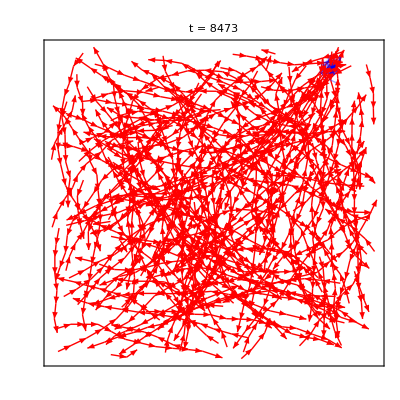

```mathematica
Show[lastframes[[1]],PlotLabel->"t = "<>ToString[simlengths[[1]]]]
```

## Shear LE

```mathematica
strains=Join[{"0.0000"},Table[ToString[SetAccuracy[i,5]],{i,0.001,0.003,0.001}]];
strains=Join[{"0.0000"},Map[ToString[SetAccuracy[#,5]]&,{0.0001,0.0004,0.0007,0.001,0.004,0.007,0.01,0.04,0.07,0.1,0.4,0.7,1}]];
basedir=archivesh<>"tri_le/";
dirs=Table[basedir<>"nbds10_strain"<>strain,{strain,strains}];
```

```mathematica
Export[archivesh<>"tri_le/t1-500.dat",as];
```

```mathematica
as=ParallelTable[ParticleTimeSeries[dr,"actins",-1,4,0,1,100],{dr,dirs}];
```

$Aborted

```mathematica
actins=Table[ToExpression[Import[dirs[[1,g]]<>"/txt_stack/actins.dat","TSV"]],{g,Length[γs]}];
```

```mathematica
a1=actins[[1]];
```

```mathematica
γs=ToExpression/@strains;
```

```mathematica
s=gs[[1]];
```

```mathematica
a2=Table[Append[a1[[j,i]],Mod[i-1,10]],{j,Length[a1]},{i,Length[a1[[j]]]}];
```

```mathematica
cbndx={-10,   10};
cbndy= {-5Sqrt[3],5Sqrt[3]};
rbnd=cbndx+20;
lbnd=cbndx-20;
ubnd=cbndy+10Sqrt[3];
dbnd=cbndy-10Sqrt[3];
```

```mathematica
trifov=10{2,Sqrt[3]};
```

```mathematica
pr=trifov*{{-0.5,0.5},{-0.5,0.5}};
```

```mathematica
fs     =simLE[a2,{},{},{},"",False,trifov,1,Blue,{0,0},s];
fsl  =simLE[a2,{},{},{},"",False,trifov,1,Blue,{-1,0},s];
fsr  =simLE[a2,{},{},{},"",False,trifov,1,Blue,{1,0},s];
fsu  =simLE[a2 ,{},{},{},"",False,trifov,1,Blue,{0,1},s];
fslu=simLE[a2, {},{},{},"",False,trifov,1,Blue,{-1,1},s];
fsru=simLE[a2, {},{},{},"",False,trifov,1,Blue,{1,1},s];fsd  =simLE[a2, {},{},{},"",False,trifov,1,Blue,{0,-1},s];
fsld=simLE[a2, {},{},{},"",False,trifov,1,Blue,{-1,-1},s];
fsrd=simLE[a2, {},{},{},"",False,trifov,1,Blue,{1,-1},s];
```

```mathematica
fsu0  =simLE[{a2[[1]]} ,{},{},{},"",False,trifov,1,Blue,{0,1},0];
fslu0=simLE[{a2[[1]]}, {},{},{},"",False,trifov,1,Blue,{-1,1},0];
fsru0=simLE[{a2[[1]]}, {},{},{},"",False,trifov,1,Blue,{1,1},0];fsd0 =simLE[{a2[[1]]}, {},{},{},"",False,trifov,1,Blue,{0,-1},0];
fsld0=simLE[{a2[[1]]}, {},{},{},"",False,trifov,1,Blue,{-1,-1},0];
fsrd0=simLE[{a2[[1]]}, {},{},{},"",False,trifov,1,Blue,{1,-1},0];
```

```mathematica
fullfs={fs,fsr,fsl,
Join[fsu0,fsu[[2;;]]],Join[fsd0,fsd[[2;;]]],
Join[fslu0,fslu[[2;;]]],Join[fsld0,fsld[[2;;]]],
Join[fsru0,fsru[[2;;]]],Join[fsrd0,fsrd[[2;;]]]}ᵀ;
```

```mathematica
drx=s*trifov[[1]];
```

```mathematica
rectbnds=Transpose/@{
{cbndx,cbndy},{rbnd,cbndy},{lbnd,cbndy},
{cbndx+drx,ubnd},{cbndx-drx,dbnd},
{lbnd+drx,ubnd},{lbnd-drx,dbnd},
{rbnd+drx,ubnd},{rbnd-drx,dbnd}};
rectbnds0=Transpose/@{
{cbndx,cbndy},{rbnd,cbndy},{lbnd,cbndy},
{cbndx,ubnd},{cbndx,dbnd},
{lbnd,ubnd},{lbnd,dbnd},
{rbnd,ubnd},{rbnd,dbnd}};
rectgfx=Table[Graphics[{EdgeForm[Directive[Thickness[0.005],Dashed,Black]],Transparent,Rectangle[rectbnds[[i,1]],rectbnds[[i,2]]]}],{i,Length[rectbnds]}];
rectgfx0=Table[Graphics[{EdgeForm[Directive[Thickness[0.005],Dashed,Black]],Transparent,Rectangle[rectbnds0[[i,1]],rectbnds0[[i,2]]]}],{i,Length[rectbnds0]}];
rectgfxt=Join[{rectgfx0},ConstantArray[rectgfx,Length[a2-1]]];
```

```mathematica
mov=Table[Show[fullfs[[t]],rectgfxt[[t]],PlotRange->{{-30-drx,30+drx},{-15Sqrt[3],15Sqrt[3]}},ImageSize->1000],{t,1,Length[fullfs],1}];
```

```mathematica
Export[archivesh<>"/n10_movie.avi",mov];
```

```mathematica
Manipulate[Show[fullfs[[t]],rectgfxt[[t]],PlotRange->{{-30-drx,30+drx},{-15Sqrt[3],15Sqrt[3]}},ImageSize->1000],{t,1,Length[fullfs],1}]
```

Part::partd: Part specification fullfs ⟦ 77 ⟧ is longer than depth of object.

Part::partd: Part specification rectgfxt ⟦ 77 ⟧ is longer than depth of object.

Show::gcomb: Could not combine the graphics objects in Show[fullfs ⟦ 77 ⟧, rectgfxt ⟦ 77 ⟧, PlotRange → {{-30 - drx, 30 + drx}, {-15\ √3, 15\ √3}}, ImageSize → 1000].

## Shear

```mathematica
strains=Join[{"0.0000"},Table[ToString[SetAccuracy[i,5]],{i,0.001,0.003,0.001}]];
strains=Join[{"0.0000"},Map[ToString[SetAccuracy[#,5]]&,{0.0001,0.0004,0.0007,0.001,0.004,0.007,0.01,0.04,0.07,0.1,0.4,0.7,1}]];
basedir=archivesh<>"tri_le/";
dirs=Table[basedir<>"nbds10_strain"<>strain,{strain,strains}];
```

```mathematica
Export[archivesh<>"tri_le/t1-500.dat",as];
```

```mathematica
as=ParallelTable[ParticleTimeSeries[dr,"actins",-1,4,0,1,100],{dr,dirs}];
```

$Aborted

```mathematica
TensorRank[{{2,2},{2,2}}]
```

2

```mathematica
a1=ParticleTimeSeries[dirs[[-3]],"actins",-1,4,0,1,100];
```

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/shear/tri_le/nbds10_strain0.4000/txt_stack/actins.txt

```mathematica
Manipulate[fs[[t]],{t,1,Length[fs],1}]
```

```mathematica
γs=ToExpression/@strains*10;
```

```mathematica
s=γs[[-3]];
```

```mathematica
a2=Table[Append[a1[[j,i]],Mod[i-1,10]],{j,Length[a1]},{i,Length[a1[[j]]]}];
```

```mathematica
fs     =sim[a2,      {},{},{},"",False,{cbndx,cbndy},1,Blue];
```

```mathematica
cbndx={-10,   10};
cbndy= {-5Sqrt[3],5Sqrt[3]};
rbnd=cbndx+20;
lbnd=cbndx-20;
ubnd=cbndy+10Sqrt[3];
dbnd=cbndy-10Sqrt[3];
```

```mathematica
boxr  =Map[(#+{20,0,0,0,0})&,a2,{2}];
boxl  =Map[(#+{-20,0,0,0,0})&,a2,{2}];
boxu  =Map[(#+{0,10Sqrt[3],0,0,0})&,a2,{2}];
boxd  =Map[(#+{0,-10Sqrt[3],0,0,0})&,a2,{2}];
boxlu=Map[(#+{-20,10Sqrt[3],0,0,0})&,a2,{2}];
boxld=Map[(#+{-20,-10Sqrt[3],0,0,0})&,a2,{2}];
boxru=Map[(#+{20,10Sqrt[3],0,0,0})&,a2,{2}];
boxrd=Map[(#+{20,-10Sqrt[3],0,0,0})&,a2,{2}];
fs     =sim[a2,      {},{},{},"",False,{cbndx,cbndy},1,Blue];
fsr  =sim[boxr,  {},{},{},"",False,{rbnd, cbndy},1,Blue];
fsl  =sim[boxl,  {},{},{},"",False,{lbnd,cbndy},1,Blue];
fsu  =sim[boxu,  {},{},{},"",False,{cbndx+s,ubnd},1,Blue];
fsd  =sim[boxd,  {},{},{},"",False,{cbndx-s,dbnd},1,Blue];
fslu=sim[boxlu,{},{},{},"",False,{lbnd+s,ubnd},1,Blue];
fsld=sim[boxld,{},{},{},"",False,{lbnd-s,dbnd},1,Blue];
fsru=sim[boxru,{},{},{},"",False,{rbnd+s,ubnd},1,Blue];
fsrd=sim[boxrd,{},{},{},"",False,{rbnd-s,dbnd},1,Blue];
```

```mathematica
boxu0  =Map[(#+{0,10Sqrt[3],0,0,0})&,{a2[[1]]},{2}];
boxd0 =Map[(#+{0,-10Sqrt[3],0,0,0})&,{a2[[1]]},{2}];
boxlu0=Map[(#+{-20,10Sqrt[3],0,0,0})&,{a2[[1]]},{2}];
boxld0=Map[(#+{-20,-10Sqrt[3],0,0,0})&,{a2[[1]]},{2}];
boxru0=Map[(#+{20,10Sqrt[3],0,0,0})&,{a2[[1]]},{2}];
boxrd0=Map[(#+{20,-10Sqrt[3],0,0,0})&,{a2[[1]]},{2}];
fsu0  =sim[boxu0,  {},{},{},"",False,{cbndx,ubnd},1,Blue];
fsd0 =sim[boxd0,  {},{},{},"",False,{cbndx,dbnd},1,Blue];
fslu0=sim[boxlu0,{},{},{},"",False,{lbnd,ubnd},1,Blue];
fsld0=sim[boxld0,{},{},{},"",False,{lbnd,dbnd},1,Blue];
fsru0=sim[boxru0,{},{},{},"",False,{rbnd,ubnd},1,Blue];
fsrd0=sim[boxrd0,{},{},{},"",False,{rbnd,dbnd},1,Blue];
```

```mathematica
fullfs={fs,fsr,fsl,
Join[fsu0,fsu[[2;;]]],Join[fsd0,fsd[[2;;]]],
Join[fslu0,fslu[[2;;]]],Join[fsld0,fsld[[2;;]]],
Join[fsru0,fsru[[2;;]]],Join[fsrd0,fsrd[[2;;]]]}ᵀ;
```

```mathematica
rectbnds=Transpose/@{
{cbndx,cbndy},{rbnd,cbndy},{lbnd,cbndy},
{cbndx+s,ubnd},{cbndx-s,dbnd},
{lbnd+s,ubnd},{lbnd-s,dbnd},
{rbnd+s,ubnd},{rbnd-s,dbnd}};
```

```mathematica
rectbnds0=Transpose/@{
{cbndx,cbndy},{rbnd,cbndy},{lbnd,cbndy},
{cbndx,ubnd},{cbndx,dbnd},
{lbnd,ubnd},{lbnd,dbnd},
{rbnd,ubnd},{rbnd,dbnd}};
```

```mathematica
rectgfx=Table[Graphics[{EdgeForm[Directive[Thickness[0.005],Dashed,Black]],Transparent,Rectangle[rectbnds[[i,1]],rectbnds[[i,2]]]}],{i,Length[rectbnds]}];
rectgfx0=Table[Graphics[{EdgeForm[Directive[Thickness[0.005],Dashed,Black]],Transparent,Rectangle[rectbnds0[[i,1]],rectbnds0[[i,2]]]}],{i,Length[rectbnds0]}];
```

```mathematica
rectgfxt=Join[{rectgfx0},ConstantArray[rectgfx,Length[a2-1]]];
```

```mathematica
fst500=Table[Show[fullfs[[t]],rectgfxt[[t]],PlotRange->{{-30-γs[[-1]],30+γs[[-1]]},{-15Sqrt[3],15Sqrt[3]}},ImageSize->1000],{t,1,Length[fullfs],1}];
```

```mathematica
Export[archivesh<>"t1-500_prob_wrong.avi",fst500];
```

$Aborted

```mathematica
Manipulate[Show[fullfs[[t]],rectgfxt[[t]],PlotRange->{{-30-γs[[-1]],30+γs[[-1]]},{-15Sqrt[3],15Sqrt[3]}},ImageSize->1000],{t,1,Length[fullfs],1}]
```

## Triangular Lattices

```mathematica
nbds=Range[10,50,10];
strains={"0.0000","0.0001","0.0004","0.0007","0.0010","0.0040","0.0070","0.0100","0.0400","0.0700","0.1000","0.4000","0.7000","1.0000"};
basedir=archivesh<>"/tri_le";
dirs=Table[basedir<>"/nbds10_strain"<>ToString[s],{s,strains}];
```

```mathematica
fs=sim[acts,{},{},{},"",False,10*{2,Sqrt[3]},0.01];
```

```mathematica
acts=ParticleTimeSeries[dirs[[-1]],"actins",-1,4,0,1,100];
```

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/shear//tri_le/nbds10_strain1.0000/txt_stack/actins.txt

```mathematica
Manipulate[fs[[t]],{t,1,Length[fs],1}]
```

Part::partd: Part specification fs ⟦ 35 ⟧ is longer than depth of object.

```mathematica
fs2=simActin[dirs[[1,-4]],100,True,10*{2,Sqrt[3]},0.01];
```

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/shear//tri_le_ythresh/nbds10_strain0.1000/txt_stack/actins.txt

Generating maxFrame frames for directory /project/weare-dinner/simonfreedman/cytomod/out/shear//tri_le_ythresh/nbds10_strain0.1000

```mathematica
Manipulate[{fs[[t]],fs2[[t]]},{t,1,Length[fs],1}]
```

## MOtility Assay

```mathematica
actins=pts[archivemot<>"mdens3x3/mdens8.0","actins_ext0-1000"];
```

```mathematica
afs=sim[actins,{},{},{},"",False,{{-100,10},{-170,0}},1];
```

```mathematica
Export[archivemot<>"mdens3x3/mdens8.0/data/movie0-100s.avi",afs];
```

```mathematica
Manipulate[Show[afs[[t]]],{t,1,Length[afs],1}]
```

Part::partd: Part specification afs ⟦ 827 ⟧ is longer than depth of object.

Show::gtype: Part is not a type of graphics.

```mathematica
actinsρ[[1,9]]
```

{{-1.47206,1.06487,0.5,0.},{-1.52511,2.04402,0.5,0.},{-1.3688,3.03684,0.5,0.},{-0.844946,3.8862,0.5,0.},{0.024538,4.37234,0.5,0.},{0.728905,5.12456,0.5,0.},{1.03332,6.06027,0.5,0.},{1.2893,6.99603,0.5,0.},{1.3986,7.98184,0.5,0.},{1.63502,8.93077,0.5,0.},{-0.87052,9.78824,0.5,0.}}

```mathematica
Manipulate[afs[[t]],{t,1,1000,1}]
```

```mathematica
ρs[[30]]
```

225

```mathematica
fs=Show[afs[[1;;-1;;2]]];
```

```mathematica
fs=Transpose[afs[[1;;-1;;2]]];
```

```mathematica
Export[archivesh<>"/L10_rho0-50.avi",fs];
```

```mathematica
Manipulate[fs[[t]],{t,1,Length[af0],1}]
```

```mathematica
archivemot ="/project/weare-dinner/simonfreedman/cytomod/out/motility/";
```

```mathematica
dxs=Flatten[Outer[Times,10^Range[-3,-1],Range[2,10]]];
```

```mathematica
fs=simSerialAM[mdwtest,100,False,{5,2},1];
```

```mathematica
acts=ParticleTimeSeries[archivemot<>"mrow/dx"<>dx,"actins",-1,4,0,1,100];
```

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/motility/mdens8/txt_stack/actins_ext.txt

```mathematica
acts100=ParticleTimeSeries[archivemot<>"mdens8","actins_ext",-1,4,99];
```

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/motility/mdens8/txt_stack/actins_ext.txt

```mathematica
acts0=ParticleTimeSeries[archivemot<>"mdens0","actins_ext",-1,4,99];
```

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/motility/mdens0/txt_stack/actins_ext.txt

```mathematica
acts01=ParticleTimeSeries[archivemot<>"mdens0_nm1","actins_ext",-1,4,99];
```

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/motility/mdens0_nm1/txt_stack/actins_ext.txt

```mathematica
Dimensions[acts100[[All,{5,10},1;;2]]ᵀ]
```

{2,101,2}

```mathematica
Length[actinsρ]
```

```mathematica
Manipulate[ListPlot[actinsρ[[i,All,1;;20;;2,1;;2]],Joined->True,PlotMarkers->Automatic,PlotRange->{{-3,3},{-3,3}},Frame->True,PlotStyle->"ThermometerColors"],{i,1,20}]
```

Part::partd: Part specification actinsρ ⟦ 1., All, 1 ;; 20 ;; 2, 1 ;; 2 ⟧ is longer than depth of object.

ListPlot::lpn: actinsρ ⟦ 1., All, 1 ;; 20 ;; 2, 1 ;; 2 ⟧ is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

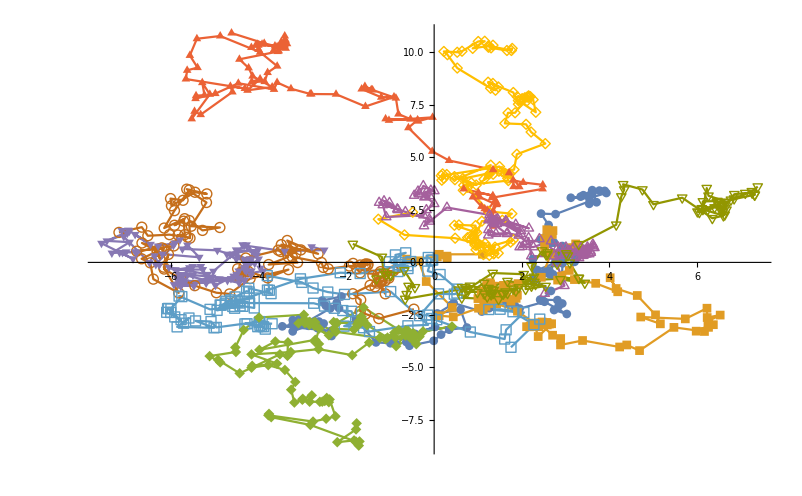

```mathematica
ListPlot[acts100[[All,1;;-1;;20,1;;2]]ᵀ,Joined->True,PlotMarkers->Automatic]
```

```mathematica
densities=ToString/@Range[50,500,50];
```

```mathematica
fs50=simActin[archivemot<>"mdens100",50,True,{2000,2000}];
```

Finished importing /project/weare-dinner/simonfreedman/cytomod/out/motility/mdens100/txt_stack/actins_ext.txt

Generating 14 frames for directory /project/weare-dinner/simonfreedman/cytomod/out/motility/mdens100

```mathematica
Manipulate[fs50[[t]],{t,1,Length[fs50],1}]
```

Part::partd: Part specification fs50 ⟦ 14 ⟧ is longer than depth of object.

## Disordered Shear Networks

```mathematica
γs=Range[0.000,0.05,0.002];
```

```mathematica
γstrs=Map[ToString[SetAccuracy[
```

```mathematica
a0=ToExpression[Import[archivesh<>"/inters_le_T0/strain0.0500/txt_stack/actins.dat","TSV"]];
l0=ToExpression[Import[archivesh<>"/inters_le_T0/strain0.0500/txt_stack/links.dat","TSV"]];
p0=pts[archivesh<>"/inters_le_T0/strain0.0500","pmotors"];
```

```mathematica
l0=pts[archivesh<>"/pre_bundled/strain0.4000","links0-100"];
```

```mathematica
l0=links[[-2]];
s=γs[[-2]];
```

```mathematica
s=0.4;
```

```mathematica
a0=Table[Append[a0[[j,i]],Mod[i-1,10]],{j,Length[a0]},{i,Length[a0[[j]]]}];
```

```mathematica
cbndx={-10,   10};
cbndy= cbndx;
rbnd=cbndx+20;
lbnd=cbndx-20;
ubnd=cbndy+20;
dbnd=cbndy-20;
```

```mathematica
fov=20{1,1};
pr=fov*{{-0.5,0.5},{-0.5,0.5}};
```

```mathematica
fs     =simLE[{},l0,{},{},"",False,fov,1,Red,{0,0},s];
fsl  =simLE[{},l0,{},{},"",False,fov,1,Red,{-1,0},s];
fsr  =simLE[{},l0,{},{},"",False,fov,1,Red,{1,0},s];
fsu  =simLE[{},l0,{},{},"",False,fov,1,Red,{0,1},s];
fslu=simLE[{}, l0,{},{},"",False,fov,1,Red,{-1,1},s];
fsru=simLE[{}, l0,{},{},"",False,fov,1,Red,{1,1},s];
fsd  =simLE[{}, l0,{},{},"",False,fov,1,Red,{0,-1},s];
fsld=simLE[{}, l0,{},{},"",False,fov,1,Red,{-1,-1},s];
fsrd=simLE[{}, l0,{},{},"",False,fov,1,Red,{1,-1},s];
```

```mathematica
fsu0  =simLE[{} ,{l0[[1]]},{},{},"",False,fov,1,Red,{0,1},0];
fslu0=simLE[{}, {l0[[1]]},{},{},"",False,fov,1,Red,{-1,1},0];
fsru0=simLE[{}, {l0[[1]]},{},{},"",False,fov,1,Red,{1,1},0];fsd0 =simLE[{}, {l0[[1]]},{},{},"",False,fov,1,Red,{0,-1},0];
fsld0=simLE[{}, {l0[[1]]},{},{},"",False,fov,1,Red,{-1,-1},0];
fsrd0=simLE[{}, {l0[[1]]},{},{},"",False,fov,1,Red,{1,-1},0];
```

```mathematica
fullfs={fs,fsr,fsl,
Join[fsu0,fsu[[2;;]]],Join[fsd0,fsd[[2;;]]],
Join[fslu0,fslu[[2;;]]],Join[fsld0,fsld[[2;;]]],
Join[fsru0,fsru[[2;;]]],Join[fsrd0,fsrd[[2;;]]]}ᵀ;
```

```mathematica
drx=s*fov[[1]];
```

```mathematica
rectbnds=Transpose/@{
{cbndx,cbndy},{rbnd,cbndy},{lbnd,cbndy},
{cbndx+drx,ubnd},{cbndx-drx,dbnd},
{lbnd+drx,ubnd},{lbnd-drx,dbnd},
{rbnd+drx,ubnd},{rbnd-drx,dbnd}};
rectbnds0=Transpose/@{
{cbndx,cbndy},{rbnd,cbndy},{lbnd,cbndy},
{cbndx,ubnd},{cbndx,dbnd},
{lbnd,ubnd},{lbnd,dbnd},
{rbnd,ubnd},{rbnd,dbnd}};
rectgfx=Table[Graphics[{EdgeForm[Directive[Thickness[0.002],Dashed,Black]],Transparent,Rectangle[rectbnds[[i,1]],rectbnds[[i,2]]]}],{i,Length[rectbnds]}];
rectgfx0=Table[Graphics[{EdgeForm[Directive[Thickness[0.002],Dashed,Black]],Transparent,Rectangle[rectbnds0[[i,1]],rectbnds0[[i,2]]]}],{i,Length[rectbnds0]}];
rectgfxt=Join[{rectgfx0},ConstantArray[rectgfx,Length[l0]-1]];
```

```mathematica
mov=Table[Show[fullfs[[t]],rectgfxt[[t]],PlotRange->{{-30-drx,30+drx},{-30,30}},ImageSize->1000],{t,1,Length[fullfs],1}];
```

```mathematica
Export[archivesh<>"/pre_bundled/strain0.4000/t1.png",mov[[2]]];
Export[archivesh<>"/pre_bundled/strain0.4000/t0.png",mov[[1]]];
```

```mathematica
mov[[2]]
```

## Motor MSD

```mathematica
mots=pts[archivemot<>"inters_motor_dense/mdens0.01","amotors"];
links=pts[archivemot<>"inters_motor_dense/mdens0.01","links"];
```

```mathematica
Length[mots]
```

77

```mathematica
Length[links]
```

113

```mathematica
links2=links[[1;;77]];
```

```mathematica
fs=sim[{},links2[[1;;-2]],{},mots[[1;;-2]],"",False,{20,20},1];
```

```mathematica
Length[fs]
```

107

```mathematica
Export[archivemot<>"inters_motor_dense/mdens0.01/data/movie.avi",fs];
```

```mathematica
Manipulate[fs[[t]],{t,1,Length[fs],10}]
```

## Active Networks

```mathematica
lprs=NumberForm[#,{2,2}]&/@Range[0.6,1,0.05];
dirs1=Table[archivef<>"/np1000_lprob/lprob"<>ToString[lp],{lp,lprs}];
(*dirs2=Table[archivef<>"/np500_lprob/lprob"<>ToString[lp],{lp,lprs}];
dirs3=Table[archivef<>"/np1000_lprob/lprob"<>ToString[lp],{lp,lprs}];*)
```

```mathematica
lprs
```

{0.60,0.65,0.70,0.75,0.80,0.85,0.90,0.95,1.00}

```mathematica
idx=15;
```

```mathematica
lksall=Table[pts[dr,"links"],{dr,dirs1}];
```

```mathematica
0
```

```mathematica
fs=ParallelTable[
sim[{},lksall[[i,1;;-2]],{},{},dirs1[[i]],True,{75,75},1,True, 16],{i,Length[dirs1]}];
```

```mathematica
Length[fs1]
```

291

```mathematica
fs1[[{100,200,Length[fs1]}]]
```

```mathematica
lks1=pts[dirs1[[idx]],"links"];
lks2=pts[dirs1[[15]],"links"];
lks3=pts[dirs1[[20]],"links"];
```

```mathematica
fs1=sim[{},lks1,{},{},dirs1[[10]],False,{75,75},1,True, 16];
fs2=sim[{},lks2,{},{},dirs1[[15]],False,{75,75},1,True, 16];
fs3=sim[{},lks3,{},{},dirs1[[20]],False,{75,75},1,True,16];
```

```mathematica
lks3=pts[dirs3[[idx]],"links"];
fs3=sim[{},lks3[[1;;-2]],{},{},dirs3[[idx]],False,{75,75},1,True,16];
```

Transpose::nmtx: The first two levels of {} cannot be transposed.

Show::shx: No graphical objects to show.

```mathematica
fs3=sim[{},lks3,{},{},dirs1[[20]],False,{75,75},1,True,16];
```

```mathematica
Export[dirs1[[20]]<>"/data/movie.avi",fs3];
```

```mathematica
fs1[[131]]
```

```mathematica
Length[fs1]
```

167

```mathematica
{fs1[[1]],fs1[[10]],fs1[[101]],fs1[[-2]]}
```

```mathematica
{fs3[[1]],fs3[[51]],fs3[[101]]}
```

```mathematica
fs1[[101]]
```

```mathematica
fs=sim[{},lks,{},{},"",False,{10,10},1];
```

```mathematica
Manipulate[Show[fs2[[t]]],{t,1,Length[fs1],1}]
```

```mathematica
frame0=Show[fs1[[1]],
ListPlot[lks1[[1,1;;-1;;10,1;;2]],PlotMarkers->{Graphics[{Blue,Disk[{0,0},1]}],0.03}]
];
```

```mathematica
Export[dirs1[[2]]<>"/frame0.png",frame0];
```

```mathematica
frameslast={Show[fs1[[-1]],
ListPlot[lks1[[-1,1;;-1;;10,1;;2]],PlotMarkers->{Graphics[{Blue,Disk[{0,0},1]}],0.03}]
],
Show[fs2[[-1]],
ListPlot[lks2[[-1,1;;-1;;10,1;;2]],PlotMarkers->{Graphics[{Blue,Disk[{0,0},1]}],0.03}]
],
Show[fs3[[-1]],
ListPlot[lks3[[-1,1;;-1;;10,1;;2]],PlotMarkers->{Graphics[{Blue,Disk[{0,0},1]}],0.03}]
]
};
```

```mathematica
Export[dirs1[[2]]<>"/framelast.png",frameslast[[1]]];
Export[dirs2[[2]]<>"/framelast.png",frameslast[[2]]];
Export[dirs3[[2]]<>"/framelast.png",frameslast[[3]]];
```

```mathematica
lks1[[1]]==lks3[[1]]
```

True

## Bending Rigidity / Cross Linker Density

```mathematica
probs=Range[0,1,0.1];
probstrs=ReplacePart[ToString[SetAccuracy[#,2]]&/@probs,1->"0.0"];
dirs1=Table[archivent<>"kb_pProb/kb0.001_pProb"<>pr,{pr,probstrs}];
dirs2=Table[archivent<>"kb_pProb/kb0.01_pProb"<>pr,{pr,probstrs}];
dirs3=Table[archivent<>"kb_pProb/kb0.1_pProb"<>pr,{pr,probstrs}];
dirs4=Table[archivent<>"kb_pProb/kb1_pProb"<>pr,{pr,probstrs}];
```

```mathematica
idx=7;
```

```mathematica
lks1=pts[dirs1[[idx]],"links"];
lks2=pts[dirs2[[idx]],"links"];
lks3=pts[dirs3[[idx]],"links"];
lks4=pts[dirs4[[idx]],"links"];
```

```mathematica
fs1=sim[{},lks1,{},{},dirs1[[idx]],False,{10,10},1,True, 11];
fs2=sim[{},lks2,{},{},dirs2[[idx]],False,{10,10},1,True, 11];
fs3=sim[{},lks3,{},{},dirs3[[idx]],False,{10,10},1,True,11];
fs4=sim[{},lks3,{},{},dirs3[[idx]],False,{10,10},1,True,11];
```

```mathematica
fs1hi=fs1; fs2hi=fs2;fs3hi=fs3;fs4hi=fs4;
```

```mathematica
fs1midlo=fs1;fs2midlo=fs2;fs3midlo=fs3;fs4midlo=fs4;
```

```mathematica
fs1midhi=fs1;fs2midhi=fs2;fs3midhi=fs3;fs4midhi=fs4;
```

```mathematica
fs1lo=fs1;fs2lo=fs2;fs3lo=fs3;fs4lo=fs4;
```

```mathematica
Manipulate[fs1[[t]],{t,1,Length[fs1],1}]
```

```mathematica
j=GraphicsGrid[{{fs4lo[[-1]],fs4midlo[[-1]],fs4midhi[[-1]],fs4hi[[-1]]},
{fs3lo[[-1]],fs3midlo[[-1]],fs3midhi[[-1]],fs3hi[[-1]]},
{fs2lo[[-1]],fs2midlo[[-1]],fs2midhi[[-1]],fs2hi[[-1]]},
{fs1lo[[-1]],fs1midlo[[-1]],fs1midhi[[-1]],fs1hi[[-1]]}},Frame->True,FrameLabel->{"Increasing CrossLinker Density ---->", "Increasing Filament Stiffness ---->"}];
```

```mathematica
Export[archivent<>"/kb_pProb/t20_p0-3-7-10_kbAll.eps",j];
```

## Force Extension Experiments

```mathematica
forces=Join[{0.001},Flatten[Table[i*10.0^j,{j,-3,3},{i,2,10}]]];
forcestrs=ToString[NumberForm[#,{5,3},ExponentFunction->(Null&)]]&/@forces;
dirs=Map[mdwpl<>"L2000_af/p"<>#&,forcestrs];
```

```mathematica
dirs[[37]]
```

/home/simonfreedman/scratch-midway/cytomod/out/pl/L2000_af/p10.000

```mathematica
lks=pts3[dirs[[37]],"links"];
```

```mathematica
pr=5000{{-0.5,0.5},{-0.5,0.5}};
```

```mathematica
frs=sim[{},lks,{},{},"out/test",False,pr,1];
```

```mathematica
Manipulate[frs[[t]],{t,1,Length[frs],1}]
```

Part::partd: Part specification frs ⟦ 56 ⟧ is longer than depth of object.